Evaluate the area under the curve y = x^2 from 1 to 3 using Riemann Sum

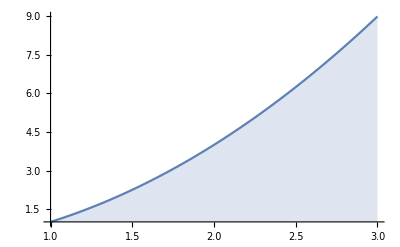

```mathematica
Plot[x^2,{x,1,3},Filling->Axis]
```

```mathematica
y[x_] := x^2
```

```mathematica
y[2]
```

4

```mathematica
delta[a_,b_,n_] := (b-a)/n
```

```mathematica
x[i_,a_,b_,n_] := a+i*delta[a,b,n]
```

Set up Riemann Sum

```mathematica
delta[0,3,10]
```

3/10

```mathematica
Sum[y[x[i,1,3,10]]*delta[1,3,10],{i,1,9}]
```

237/25

```mathematica
N[Sum[y[x[i,1,3,100]]*delta[1,3,100],{i,1,99}]]
```

8.5668

```mathematica
rsum[n_] := N[Sum[y[x[i,1,3,n]]*delta[1,3,n],{i,1,n-1}]]
```

```mathematica
rsum[100]
```

8.5668

```mathematica
Table[10 i+j,{i,4},{j,3}]
```

{{11,12,13},{21,22,23},{31,32,33},{41,42,43}}

```mathematica
Table[10 i+j,{i,4},{j,3}];
MatrixForm[%]
```

(11 | 12 | 13
21 | 22 | 23
31 | 32 | 33
41 | 42 | 43)